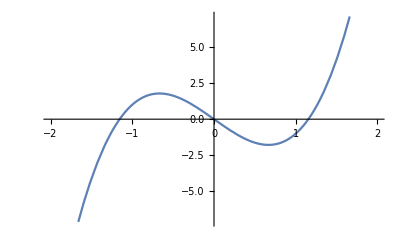

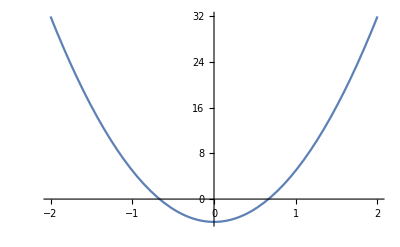

```mathematica
p[a_,x_] := x^3 - a*x
f[a_,x_] := (x^4)/4 - (x^2)*a/2
alpha[p_,r_] := ArcCos[(4*p)/(r^3)]/3
 
(* b= -20;
para = ParametricPlot[{p[b,t],f[b,t]},{t,-1,1}];
reg1 = Plot[p[b,x],{x,-100,100}];
reg2 =Plot[f[b,x], {x,-100,100}];
Show[reg1,reg2]; *)

(* p versus f(x)-p*x --> like f(p)-p*x ?*)
Animate[ParametricPlot[{p[a,t],f[a,t]-p[a,t]*t},{t,-2,2}],{a,-3,3, Appearance->"Labeled"},AnimationRunning->True]

Animate[ParametricPlot[{p[a,t],f[a,]-p[a,t]*t},{t,-2,2}],{a,-3,3, Appearance->"Labeled"},AnimationRunning->True]
(* now plot p versus f(x(alpha(p))-p*x(alpha(p)) *)
Plot[3x^3 - 4x, {x,-2,2}]
Plot[9x^2 - 4, {x,-2,2}]
```